```mathematica
ClearAll["Global`*"]
```

# Some functions

```mathematica
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
compileOptionsPar={Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\Omega","\\Delta"},Evaluate@font,ColorFunction->"SunsetColors"};plotOptions={Frame->True,PerformanceGoal->"Quality",Evaluate@font,FrameLabel->MaTeX/@{"\\Omega","\\Delta"},Axes->False};getTimeFromSolve[list_]:=list[[1,2,2,1,1,2]]
PlotSol[sol_,col_:"Green"]:=ParametricPlot[
{a[t],b[t]}/.sol,{t,0,getTimeFromSolve[sol]}
,PlotRange->All,Frame->True,Evaluate@plotOptions,PlotStyle->ToExpression@col,AspectRatio->1]
```

```mathematica
dim=2;
H[Ω_,Δ_]:={{Ω,Δ},{Δ,-Ω}}
DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
g[λ_,χ_]:=Module[{g11,g12,g22,energies,eigenvectors,enNonSort,eigNonSort},
{enNonSort,eigNonSort}=Eigensystem[H[λ,χ]];
{energies,eigenvectors}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
g11=Re@Sum[((Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH1[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g12=Re@Sum[(Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]]Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]])/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g22=Re@Sum[((Conjugate[eigenvectors[[1]]].DH2[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
Fidelity[bra_,ket_]:=Norm[Conjugate[bra].ket]^2
eigenvectorsSorted[Ω_,Δ_,t_]:=Module[{H,enNonSort,eigNonSort,energies,eig},
H={{Ω,Δ},{Δ,-Ω}};
{enNonSort,eigNonSort}=Eigensystem[H];
{energies,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
Map[Normalize,eig]
]
eigSortedHfunction[H_]:=Module[{enNonSort,eigNonSort,energies,eig},
{enNonSort,eigNonSort}=Eigensystem[H];
{energies,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
Map[Normalize,eig]
]
```

# Parametric space vizualizations

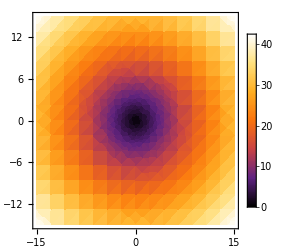

```mathematica
enPlot=DensityPlot[Differences[Eigenvalues@H[Ω,Δ]][[1]],{Ω,-15,15},{Δ,-15,15},Evaluate@densityPlotOptions,ImageSize->250]
```

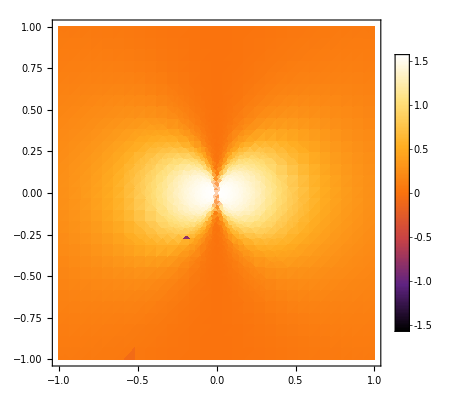

```mathematica
DensityPlot[ArcTan@g[Ω,Δ],{Ω,-1,1},{Δ,-1,1},Evaluate@densityPlotOptions,PlotPoints->30,PerformanceGoal->"Quality",Exclusions->None]
```

# Reconstructing the problem from Geodesic Paths for Quantum Many - Body Systems

## Defining different drivings

### Geodesic

```mathematica
Ωscale=10;
θ[t_]:=π t 
Ω[t_]:=-Ωscale Cos@θ[t]
Δ[t_]:=Ωscale Sin@θ[t]
```

### Linear

```mathematica
Ωscale=10;
Ωl[t_]:=Ωscale (-1+2 t)
Δl[t_]:=0.3
```

### How does it look like?

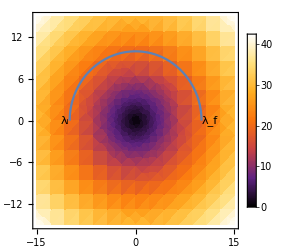

```mathematica
drivingFig=Show[{
enPlot,
ParametricPlot[{Ω[t],Δ[t]},{t,0,1}],
(*ParametricPlot[{Ωl[t],Δl[t]},{t,0,1},PlotStyle->Dashed],*)
Graphics[Text["λ_i",{Ω[0],Δ[0]},{1.5,0}]],
Graphics[Text["λ_f",{Ω[1],Δ[1]},{-1.5,0}]]
}]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/driving.pdf",drivingFig,"AllowRasterization"->True,ImageResolution->800];
```

## Numerical fidelity

Functions input are two 1 - parametric functions of time, defining the driving, and t as time, or Tf as final time .
Output is function value and norm of vector, for numerical precision control.

```mathematica
FidPlot[Ω1_,Δ1_,Tf_]:=Module[{Ω,Δ,H,eig,Ψ,a,b,sol,t},
Ω[t_]:=Ω1[t/Tf];
Δ[t_]:=Δ1[t/Tf];
H[t_]:={{Ω[t],Δ[t]},{Δ[t],-Ω[t]}};
eig[t_]:=eigenvectorsSorted[Ω[t],Δ[t],t];
Ψ[t_]={a[t],b[t]};
sol=NDSolve[{I Ψ'[t]==H[t].Ψ[t],Ψ[0]=={1,0}},Ψ[t],{t,0,Tf},Method->{"TimeIntegration"->{"ExplicitRungeKutta"}}];
{Plot[1-Fidelity[Flatten[Ψ[t]/.sol],eig[t][[1]]],{t,0,Tf},Evaluate@font,Frame->True,FrameLabel->{"t","1-F"},ImageSize->Medium],
Plot[Norm[Evaluate[Ψ[t]/.sol]],{t,0,Tf},Evaluate@font,Frame->True,FrameLabel->{"t","|Ψ(t)|"},ImageSize->Medium]}
]
FidFinal[Ω1_,Δ1_,Tf_]:=Module[{Ω,Δ,H,eig,Ψ,a,b,sol,t},
Ω[t_]:=Ω1[t/Tf];
Δ[t_]:=Δ1[t/Tf];
H[t_]:={{Ω[t],Δ[t]},{Δ[t],-Ω[t]}};
eig[t_]:=eigenvectorsSorted[Ω[t],Δ[t],t];
Ψ[t_]={a[t],b[t]};
sol=NDSolve[{I Ψ'[t]==H[t].Ψ[t],Ψ[0]=={1,0}},Ψ[t],{t,0,Tf},Method->{"TimeIntegration"->{"ExplicitRungeKutta"}}];
1-Fidelity[Flatten[Ψ[t]/.sol]/.t->Tf,eig[Tf][[1]]]

]
```

## Results: Linear driving

### Fidelity in time with error

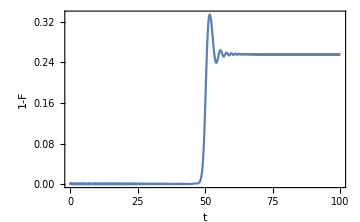
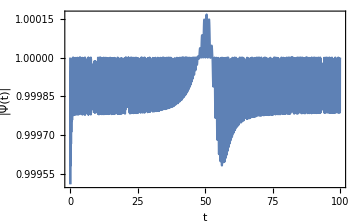

```mathematica
FidPlot[Ωl,Δl,100]
```

### Probability of non - excitation

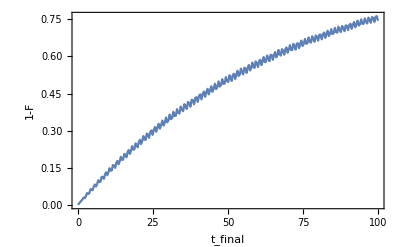

```mathematica
Plot[1-FidFinal[Ωl,Δl,tfinal],{tfinal,0.01,100},PlotRange->All,PlotPoints->5,Evaluate@font,Frame->True,FrameLabel->{"t_final","1-F"}]
```

### Result from the paper - fidelity dependence on Tf

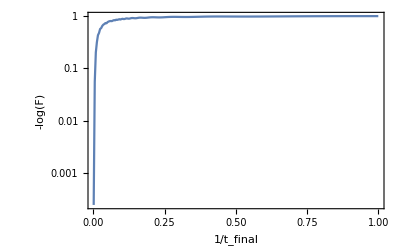

```mathematica
Plot[FidFinal[Ωl,Δl,1/trev],{trev,0.001,1},PlotRange->All,PlotPoints->5,ScalingFunctions->"Log",Evaluate@font,Frame->True,FrameLabel->{"1/t_final","-log(F)"}]
```

### Felipe-like result

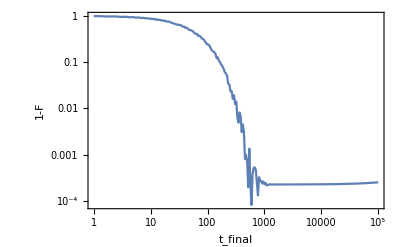

```mathematica
Plot[FidFinal[Ωl,Δl,tfinal],{tfinal,1,10^5},PlotRange->All,ScalingFunctions->{"Log","Log"},PlotPoints->5,Evaluate@font,Frame->True,FrameLabel->{"t_final","1-F"}]
```

## Results: Geodesic driving (half-sphere)

### Fidelity in time with error

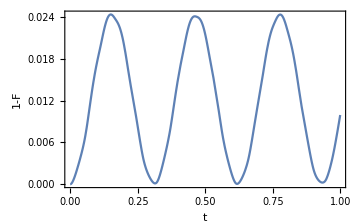
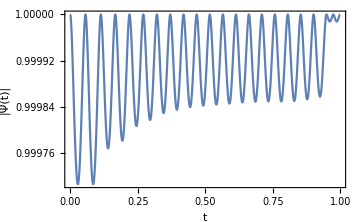

```mathematica
FidPlot[Ω,Δ,1]
```

### Probability of non - excitation

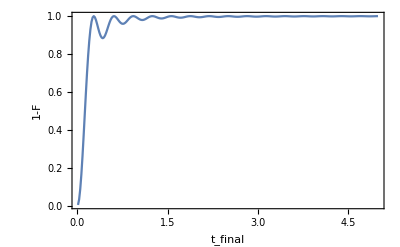

```mathematica
Plot[1-FidFinal[Ω,Δ,tfinal],{tfinal,0.01,5},PlotRange->All,PlotPoints->5,Evaluate@font,Frame->True,FrameLabel->{"t_final","1-F"}]
```

### Result from the paper - fidelity dependence on Tf

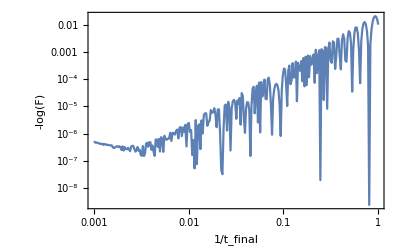

```mathematica
Plot[FidFinal[Ω,Δ,1/trev],{trev,0.001,1},PlotRange->All,PlotPoints->5,ScalingFunctions->{"Log","Log"},Evaluate@font,Frame->True,FrameLabel->{"1/t_final","-log(F)"}]
```

### Infidelity dependence on Tf - loglog

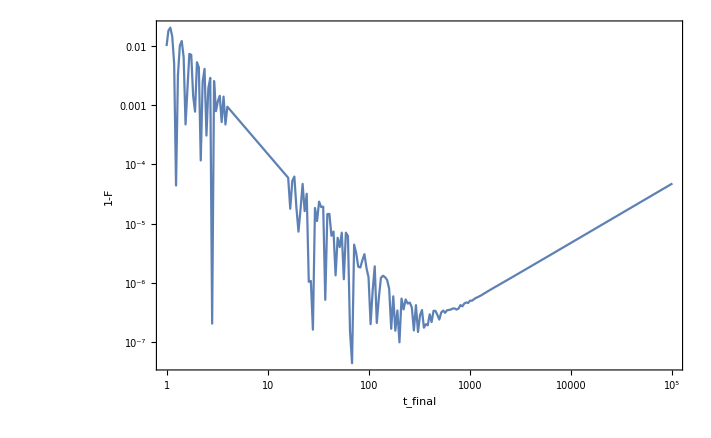

```mathematica
Plot[FidFinal[Ω,Δ,tfinal],{tfinal,1,10^5},PlotRange->All,ScalingFunctions->{"Log","Log"},PlotPoints->5,Evaluate@font,Frame->True,FrameLabel->{"t_final","1-F"}]
```

## Exact solution for circular driving

```mathematica
σ={{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
Hpurple[t_,Tf_]:={-s Cos[ω[Tf] t],0,s Sin[ω[Tf] t]}.σ
Hblue[t_,Tf_]:={{-ω[Tf]/2,-s},{-s,ω[Tf]/2}}
```

## Some calculations along the way

```mathematica
σ={{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
d[t_,s_,Tf_]:={-s Cos[π t/Tf],0,s Sin[π t/Tf]}
```

```mathematica
Hc[t_]:=d[t,10,100].σ
```

```mathematica
HH={-s Cos[ω t],0,s Sin[ω t]}.σ
MatrixExp[I ω t σ[[2]]/2].HH.MatrixExp[-I ω t σ[[2]]/2]//FullSimplify//MatrixForm
```

{{s Sin[t ω],-s Cos[t ω]},{-s Cos[t ω],-s Sin[t ω]}}

(0 | -s
-s | 0)

```mathematica
HH//MatrixForm
```

(s Sin[t ω] | -s Cos[t ω]
-s Cos[t ω] | -s Sin[t ω])

```mathematica
Eigensystem[HH]
```

{{-s,s},{{Sec[t ω]-Tan[t ω],1},{-Sec[t ω]-Tan[t ω],1}}}

```mathematica
Hblue={{-ω/2,-s},{-s,ω/2}};
Ublue=MatrixExp[-I Hblue t]//FullSimplify
```

{{Cos[1/2 t √(4 s^2+ω^2)]+(ⅈ ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))},{(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),Cos[1/2 t √(4 s^2+ω^2)]-(ⅈ ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}}

```mathematica
U=MatrixExp[-I ω t σ[[2]]/2].Ublue.MatrixExp[I ω t σ[[2]]/2]//FullSimplify
```

{{Cos[1/2 t √(4 s^2+ω^2)]+(ⅈ (ω Cos[t ω]-2 s Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),(ⅈ (2 s Cos[t ω]+ω Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))},{(ⅈ (2 s Cos[t ω]+ω Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),Cos[1/2 t √(4 s^2+ω^2)]+(ⅈ (-ω Cos[t ω]+2 s Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}}

```mathematica
U//MatrixForm
```

```mathematica
({{Cos[q t]+(ⅈ (ω Cos[t ω]-2 s Sin[t ω]) Sin[qt])/(2q), (ⅈ (2 s Cos[t ω]+ω Sin[t ω]) Sin[qt])/(2q)}, {(ⅈ (2 s Cos[t ω]+ω Sin[t ω]) Sin[qt])/(2q), Cos[qt]+(ⅈ (-ω Cos[t ω]+2 s Sin[t ω]) Sin[qt])/(2q)}})
```

```mathematica
N@Det[Ublue/.{t->1,s->10,ω->10}]
```

1.

```mathematica
N@Norm[Ublue.{1,0}/.{t->1,s->10,ω->10}]
```

1.

```mathematica
{en,{eig0,eig1}}=Eigensystem[{{-ω/2,-s},{-s,ω/2}}]
```

{{-1/2 √(4 s^2+ω^2),1/2 √(4 s^2+ω^2)},{{-(-ω-√(4 s^2+ω^2))/(2 s),1},{-(-ω+√(4 s^2+ω^2))/(2 s),1}}}

```mathematica
MatrixExp[I t {{-ω/2,-s},{-s,ω/2}}]//FullSimplify
```

{{Cos[1/2 t √(4 s^2+ω^2)]-(ⅈ ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),-(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))},{-(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),Cos[1/2 t √(4 s^2+ω^2)]+(ⅈ ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}}

```mathematica
which is for e=1/2 t q, q=√(4 s^2+ω^2)
```

```mathematica
{{Cos[e]-(ⅈ ω Sin[e])/q,-(2 ⅈ s Sin[e])/q},{-(2 ⅈ s Sin[e])/q,Cos[e]+(ⅈ ω Sin[e])/q}}
```

```mathematica
s=1;
ω[Tf_]:=π/Tf
d[t_,Tf_]:={-s Cos[ω[Tf]t],0,s Sin[ω[Tf]t]}
```

```mathematica
(*σ={{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
d[t_,s_,Tf_]:={-s Cos[π t/Tf],0,s Sin[π t/Tf]}
Hc[t_,Tf_]:=d[t,Tf].σ*)
```

```mathematica
(*eigsOriginalFrame[t_,Tf_]:=Map[Normalize,Eigenvectors[Hc[t,Tf]]]*)
```

```mathematica
ens[Tf_]:=Eigenvalues[{{-ω[Tf]/2,-s},{-s,ω[Tf]/2}}]
eigs[Tf_]:=Eigenvectors[{{-ω[Tf]/2,-s},{-s,ω[Tf]/2}}]
psi[t_,Tf_]:=MatrixExp[-I/2 ω[Tf]t σ[[2]]].MatrixExp[I {{-ω[Tf]/2,-s},{-s,ω[Tf]/2}} t].{0,1}
(*ground[t_,Tf_]:=MatrixExp[-I/2 ω[Tf] t σ[[2]]].{0,1}*)
excitationProbability[t_,Tf_]:=Fidelity[{0,1},MatrixExp[I {{-ω[Tf]/2,-s},{-s,ω[Tf]/2}} t].{0,1}]
```

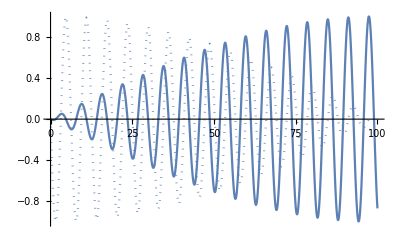

```mathematica
ReImPlot[psi[t,100][[1]],{t,0,100}]
```

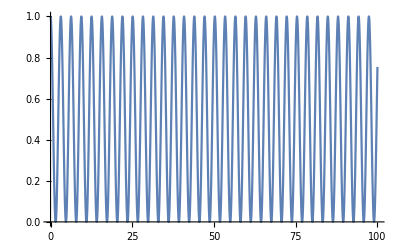

```mathematica
Plot[excitationProbability[t,100],{t,0,100}]
```

## Results

Fidelity is time (t) and final time (Tf) dependent

```mathematica
s=10;
ω[Tf_]:=π/Tf
(*f[t_,Tf_]:=1-(1+ω[Tf]^2/(4 s^2))^-1 Sin[√(4 s^2-ω[Tf]^2)t/2]^2*)
```

#### Purple basis

```mathematica
Upurple[t_,Tf_]:={{Cos[1/2 t √(4 s^2+ω[Tf]^2)]+(ⅈ ω[Tf] Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2)),(2 ⅈ s Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2))},{(2 ⅈ s Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2)),Cos[1/2 t √(4 s^2+ω[Tf]^2)]-(ⅈ ω[Tf] Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2))}}
```

```mathematica
groundStatepurple[t_,Tf_]:=eigSortedHfunction[Hpurple[t,Tf]][[1]]
psipurple[t_,Tf_]:=Upurple[t,Tf].groundStatepurple[0,Tf]
fpurple[t_,Tf_]:=Fidelity[groundStatepurple[t,Tf],psipurple[t,Tf]]
```

#### Blue basis

```mathematica
Ublue[t_,Tf_]:={{Cos[1/2 t √(4 s^2+ω[Tf]^2)]+(ⅈ (ω[Tf] Cos[t ω[Tf]]-2 s Sin[t ω[Tf]]) Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2)),(ⅈ (2 s Cos[t ω[Tf]]+ω[Tf] Sin[t ω[Tf]]) Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2))},{(ⅈ (2 s Cos[t ω[Tf]]+ω[Tf] Sin[t ω[Tf]]) Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2)),Cos[1/2 t √(4 s^2+ω[Tf]^2)]+(ⅈ (-ω[Tf] Cos[t ω[Tf]]+2 s Sin[t ω[Tf]]) Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2))}}
```

```mathematica
groundStateblue[t_,Tf_]:=eigSortedHfunction[Hblue[t,Tf]][[1]]
psiblue[t_,Tf_]:=Ublue[t,Tf].groundStateblue[0,Tf]
fblue[t_,Tf_]:=Fidelity[groundStateblue[t,Tf],psiblue[t,Tf]]
```

### Analytical simplification

```mathematica
Clear[ω]
Clear[s]
```

```mathematica
f[t,Tf]//FullSimplify
```

```mathematica
Norm[(ⅈ Sin[q] (s Cos[t ω]+Sin[t ω] ω/2))/q]^2
```

```mathematica
psi[t,Tf]
```

```mathematica
{Cos[qt]+(ⅈ Sin[qt] (-s Sin[t ω(T_f)]+Cos[t ω(T_f)](ω(T_f))/2))/1,(ⅈ Sin[qt] (s Cos[t ω(T_f)]+Sin[t ω(T_f)] (ω(T_f))/2))/q}
```

### Infidelity in time with error

```mathematica
f[t_,Tf_]:=fpurple[t,Tf]
```

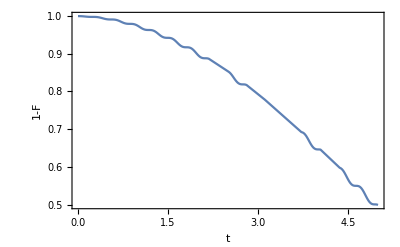

```mathematica
Plot[f[t,10],{t,0,5},PlotRange->All,PlotPoints->5,Evaluate@font,Frame->True,FrameLabel->{"t","1-F"}]
```

### Probability of non - excitation

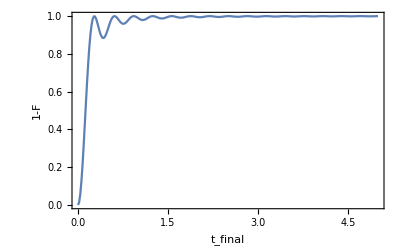

```mathematica
Plot[1-f[Tf,Tf],{Tf,0,5},PlotRange->All,PlotPoints->5,Evaluate@font,Frame->True,FrameLabel->{"t_final","1-F"}]
```

### Result from the paper - fidelity dependence on Tf

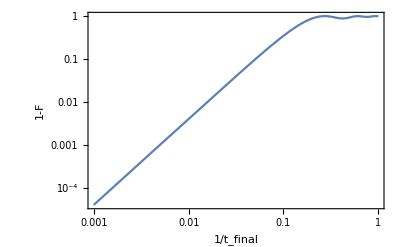

```mathematica
Plot[1-f[trev,trev],{trev,0.001,1},PlotRange->All,PlotPoints->5,ScalingFunctions->{"Log","Log"},Evaluate@font,Frame->True,FrameLabel->{"1/t_final","1-F"}]
```

### Infidelity dependence on Tf - loglog

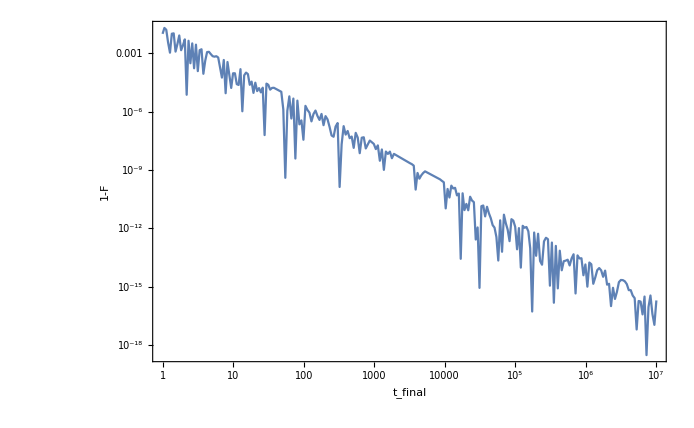

```mathematica
Plot[f[Tf,Tf],{Tf,1,10^7},PlotRange->All,ScalingFunctions->{"Log","Log"},PlotPoints->5,Evaluate@font,Frame->True,FrameLabel->{"t_final","1-F"}]
```